# Human_corona blast hit

```mathematica
(*base="/Users/kouamano/"*)
```

```mathematica
base="/home/kamano/"
```

/home/kamano/

## Program

```mathematica
Get[base<>"gitsrc/MATH_SCRIPT/SCRIPTS/String_operations.txt"]
```

```mathematica
createAnnotationHit[blast_]:=Module[{head,body},
head=blast[[1]];
body=Drop[blast,1];
Map[{head,#}&,body]
]
```

```mathematica
getSbjctLine[antn_]:=StringCases[antn,RegularExpression["Sbjct:.*"]]
```

```mathematica
mergeSbjctLine[sbjct_]:=Module[{start,end,body,seq},
body=Map[StringSplit[StringDrop[#,7]]&,sbjct];
start=body[[1,1]];
end=body[[-1,3]];
seq=StringReplace[StringJoin[Map[#[[2]]&,body]],"-"->""];
{start,seq,end}
]
```

```mathematica
getQueryLine[antn_]:=StringCases[antn,RegularExpression["Query:.*"]]
```

```mathematica
mergeQueryLine=mergeSbjctLine
```

mergeSbjctLine

```mathematica
mergeAnnotationSbjct[antn_]:=Module[{head,strand,expect,ident,sbjctArr,queryArr,sbjctSeq,querySeq},
head=antn[[1]];
head=StringReplace[head,"\n"->" "];
strand = StringCases[antn[[2]],RegularExpression["Strand = .*"]];
strand = StringReplace[strand,"\n"->" "];
expect = StringCases[antn[[2]],RegularExpression["Expect = .*"]];
expect = StringReplace[expect,"\n"->" "];
ident= StringCases[antn[[2]],RegularExpression["Identities = .*"]];
ident =  StringReplace[ident,"\n"->" "];
sbjctArr=getSbjctLine[antn[[2]]];
sbjctSeq=mergeSbjctLine[sbjctArr];
sbjctSeq = StringReplace[sbjctSeq,"\n"->""];
queryArr=getQueryLine[antn[[2]]];
querySeq=mergeSbjctLine[queryArr];
querySeq = StringReplace[querySeq,"\n"->""];
Flatten[{head,"Query: ",querySeq[[1]],querySeq[[3]],expect,ident,strand,sbjctSeq}]
]
```

```mathematica
createFastaFromAnnotationSbjct[sbjct_]:=">s"<>sbjct[[1]]<>"|"<>sbjct[[2]]<>sbjct[[3]]<>" -- "<>sbjct[[4]]<>"|"<>sbjct[[5]]<>"; "<>sbjct[[6]]<>"; "<>sbjct[[7]]<>"; "<>sbjct[[8]]<>" -- "<>sbjct[[10]]<>"\n"<>sbjct[[9]]<>"\n"
```

```mathematica
inRegion[{s_,e_},n_]:=If[s≤n && n ≤ e,1,0]
```

## Basic information of Human corona virus

```mathematica
fasta["corona"]=Import["/BANK/genome/human_corona/Wuhan_corona.fna","FASTA"];
```

```mathematica
len["corona"]=fasta["corona"][[1]]//StringLength
```

29903

```mathematica
skipBase=200
```

200

### Coding region (corona)

```mathematica
cdsstr=Import["/BANK/genome/human_corona/Wuhan_corona.gene.reg","TEXT"];
```

```mathematica
cds=Map[ToExpression["{"<>#<>"}"]&,StringSplit[cdsstr,"\n"]]
```

{{266,21555},{21563,25384},{25393,26220},{26245,26472},{26523,27191},{27202,27387},{27394,27759},{27894,28259},{28274,29533},{29558,29674}}

```mathematica
Map[Head,cds,{2}]//Tally
```

{{{Integer,Integer},10}}

### Coding position (corona)

```mathematica
cdsS=Map[Point[{#[[1]],-100+25}]&,cds]
```

{Point[{266,-75}],Point[{21563,-75}],Point[{25393,-75}],Point[{26245,-75}],Point[{26523,-75}],Point[{27202,-75}],Point[{27394,-75}],Point[{27894,-75}],Point[{28274,-75}],Point[{29558,-75}]}

```mathematica
cdsE=Map[Point[{#[[2]],-100-25}]&,cds]
```

{Point[{21555,-125}],Point[{25384,-125}],Point[{26220,-125}],Point[{26472,-125}],Point[{27191,-125}],Point[{27387,-125}],Point[{27759,-125}],Point[{28259,-125}],Point[{29533,-125}],Point[{29674,-125}]}

```mathematica
cdsM=Point[{13468,-100}]
```

Point[{13468,-100}]

```mathematica
Graphics[cdsSG={RGBColor[1,0,0],cdsS}]
```

-Graphics-

```mathematica
Graphics[cdsEG={RGBColor[0,0,1],cdsE}]
```

-Graphics-

```mathematica
cdsMG={RGBColor[0,1,0],cdsM}
```

{RGBColor[0, 1, 0],Point[{13468,-100}]}

```mathematica
cdsLine=Map[Line[{{#[[1]],-100},{#[[2]],-100}}]&,cds]
```

{Line[{{266,-100},{21555,-100}}],Line[{{21563,-100},{25384,-100}}],Line[{{25393,-100},{26220,-100}}],Line[{{26245,-100},{26472,-100}}],Line[{{26523,-100},{27191,-100}}],Line[{{27202,-100},{27387,-100}}],Line[{{27394,-100},{27759,-100}}],Line[{{27894,-100},{28259,-100}}],Line[{{28274,-100},{29533,-100}}],Line[{{29558,-100},{29674,-100}}]}

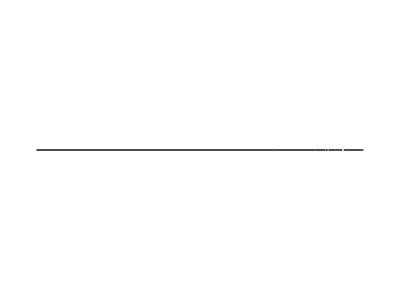

```mathematica
Graphics[cdsLine]
```

### Self correlation (corona)

```mathematica
qqText=Import["/BANK/genome/human_corona/Q_Q_W10.hitframe","Text"];
```

```mathematica
qqTextSpl=StringSplit[qqText,"Query= "];
```

```mathematica
qqMap=Map[StringReplace[#,RegularExpression["^.*_"]->""]&,Map[StringSplit[#,">"]&,qqTextSpl],{2}]//ToExpression
```

{{1,1,2,3,4013,4012,4011,4},{2,2,3,1,4,5},{3,3,4,2,5,1,2582,2581,2580,2579,2237,2236,2235,538,537,536,535,6},{4,4,5,3,6,2,1203,1202,1201,2582,2581,2580,2579,2237,2236,2235,538,537,536,535,7,1},{5,5,6,4,7,3,1203,1202,1201,2582,2581,2580,2579,2237,2236,2235,538,537,536,535,8,2},{6,6,7,5,8,4,1203,1202,1201,9,3},{7,7,8,6,9,5,10,4},5963,{5971,5971,5972,5970,5973,5969,5974,5968},{5972,5972,5971,5970,5973,5969},{5973,5973,5972,5971,5970},{5974},{5975},{5976}}
 |  |  |  |

```mathematica
Cases[qqMap,x_/;Length[x]==1]
```

{{2214},{5974},{5975},{5976}}

```mathematica
qqReMap=Map[If[Length[#]==1,{#[[1]],#[[1]]}*5,#*5]&,qqMap];
```

```mathematica
qqReMap[[1]]
```

{5,5,10,15,20065,20060,20055,20}

```mathematica
(slefCorrCount=Sort[Map[Drop[#,1]&,qqReMap]//Flatten//Tally,#[[1]]≤#2[[1]]&])//Length
```

5976

```mathematica
slefCorrCount[[1]]
```

{5,7}

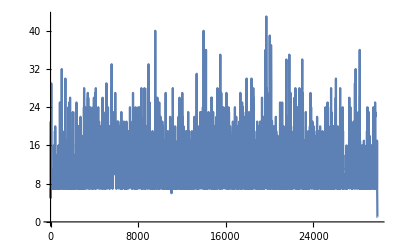

```mathematica
ListPlot[slefCorrCount,Joined->True,PlotRange->Full]
```

```mathematica
Sort[Map[#[[2]]&,slefCorrCount]//Tally,#1[[1]]<#2[[1]]&]
```

{{1,2},{2,1},{4,1},{5,2},{6,2},{7,1519},{8,4},{10,1258},{11,443},{12,7},{13,655},{14,488},{15,94},{16,313},{17,324},{18,130},{19,138},{20,186},{21,83},{22,62},{23,64},{24,51},{25,30},{26,30},{27,27},{28,21},{29,5},{30,6},{31,6},{32,2},{33,4},{34,5},{35,2},{36,4},{37,2},{39,1},{40,3},{43,1}}

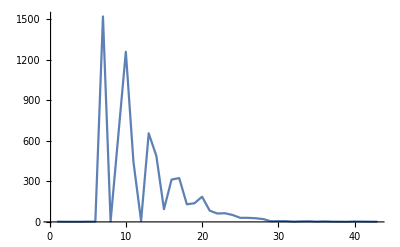

```mathematica
ListPlot[Sort[Map[#[[2]]&,slefCorrCount]//Tally,#1[[1]]<#2[[1]]&],Joined->True,PlotRange->Full]
```

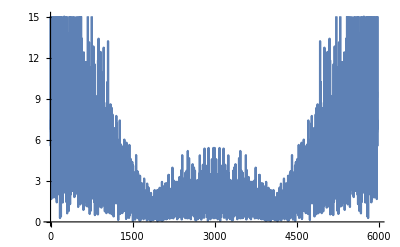

```mathematica
ListPlot[Abs[Fourier[Map[#[[2]]&,slefCorrCount]]],Joined->True]
```

```mathematica
reMapToPoint[l_]:=Block[{h,t},
h=l[[1]];
t=Drop[l,1];
Map[{h,#}&,t]
]
```

```mathematica
selfCorrPoint=Map[Point[#+{0,-1000}]&,Flatten[Map[reMapToPoint[#]&,qqReMap],1]];
```

```mathematica
Graphics[{Gray,PointSize->0.002,selfCorrPoint}]
```

-Graphics-

```mathematica
slefCorrCount//Short
```

{{5,7},{10,5},{15,17},{20,21},{25,21},{30,10},{35,7},«5962»,{29850,14},{29855,6},{29860,5},{29865,4},{29870,2},{29875,1},{29880,1}}

```mathematica
Nearest[Map[#[[1]]&,slefCorrCount]->slefCorrCount,1000]
```

{{1000,7}}

## Vertebrate :: corona

```mathematica
vertebra={"Bat","Beluga","Camel","Cat","C_lupus_familiaris","Ferret","Human","Mouse","Rabbit","S_scrofa","RockPigeon","Turkey"}
```

{Bat,Beluga,Camel,Cat,C_lupus_familiaris,Ferret,Human,Mouse,Rabbit,S_scrofa,RockPigeon,Turkey}

## Full (Bat) :: Full (corona)

```mathematica
Idt["Bat","F","F"]=Import["/BANK/genome/human_corona/Bat-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["Bat","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["Bat","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["Bat","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["Bat","F","F"]]]];
```

```mathematica
hitLenSource["Bat","F","F"]//Length
```

26

```mathematica
Max[hitLenSource["Bat","F","F"]]
Min[hitLenSource["Bat","F","F"]]
```

29

22

### Hit sequence

```mathematica
blast["Bat","F","F"]=Import["/BANK/genome/human_corona/Bat-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["Bat","F","F"]=Drop[StringSplit[blast["Bat","F","F"],">"],1];
```

```mathematica
blasteach["Bat","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["Bat","F","F"] ];
```

```mathematica
annotationHit["Bat","F","F"]=Flatten[Map[createAnnotationHit,blasteach["Bat","F","F"]],1];
```

```mathematica
hitCount["Bat","F","F"]=Length[annotationHit["Bat","F","F"]]
```

26

```mathematica
hitFragment["Bat","F","F"]=Table[mergeAnnotationSbjct[annotationHit["Bat","F","F"][[i]]],{i,hitCount["Bat","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["Bat","F","F"]]//Length
```

26

### Hit position

```mathematica
QhitPosition["Bat","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200},{#[[4]]//ToExpression,200}}&,hitFragment["Bat","F","F"]]];
```

```mathematica
Map[Head,QhitPosition["Bat","F","F"],{3}]//Flatten//Tally
```

{{Integer,104}}

```mathematica
QhitLine["Bat","F","F"]={Map[Line,QhitPosition["Bat","F","F"],{1}],Text[Style["Bat",12],{0,200},{1,0}]};
```

```mathematica
Graphics[QhitLine["Bat","F","F"]]
```

-Graphics-

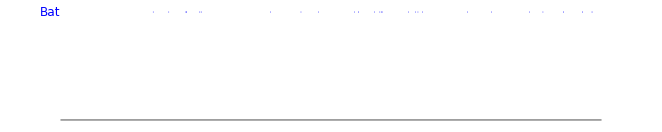

```mathematica
Graphics[{RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Full (Beluga) :: Full (corona)

```mathematica
Idt["Beluga","F","F"]=Import["/BANK/genome/human_corona/Beluga-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["Beluga","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["Beluga","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["Beluga","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["Beluga","F","F"]]]];
```

```mathematica
hitLenSource["Beluga","F","F"]//Length
```

28

```mathematica
Max[hitLenSource["Beluga","F","F"]]
Min[hitLenSource["Beluga","F","F"]]
```

31

22

### Hit sequence

```mathematica
blast["Beluga","F","F"]=Import["/BANK/genome/human_corona/Beluga-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["Beluga","F","F"]=Drop[StringSplit[blast["Beluga","F","F"],">"],1];
```

```mathematica
blasteach["Beluga","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["Beluga","F","F"] ];
```

```mathematica
annotationHit["Beluga","F","F"]=Flatten[Map[createAnnotationHit,blasteach["Beluga","F","F"]],1];
```

```mathematica
hitCount["Beluga","F","F"]=Length[annotationHit["Beluga","F","F"]]
```

28

```mathematica
hitFragment["Beluga","F","F"]=Table[mergeAnnotationSbjct[annotationHit["Beluga","F","F"][[i]]],{i,hitCount["Beluga","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["Beluga","F","F"]]//Length
```

28

### Hit position

```mathematica
QhitPosition["Beluga","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*2},{#[[4]]//ToExpression,200*2}}&,hitFragment["Beluga","F","F"]]];
```

```mathematica
Map[Head,QhitPosition["Beluga","F","F"],{3}]//Flatten//Tally
```

{{Integer,112}}

```mathematica
QhitLine["Beluga","F","F"]={Map[Line,QhitPosition["Beluga","F","F"],{1}],Text[Style["Beluga",12],{0,200*2},{1,0}]};
```

```mathematica
Graphics[QhitLine["Beluga","F","F"]]
```

-Graphics-

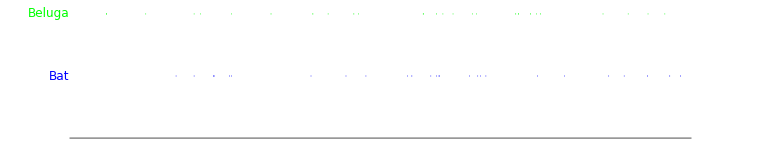

```mathematica
Graphics[{RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Full (Camel) :: Full (corona)

```mathematica
Idt["Camel","F","F"]=Import["/BANK/genome/human_corona/Camel-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["Camel","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["Camel","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["Camel","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["Camel","F","F"]]]];
```

```mathematica
hitLenSource["Camel","F","F"]//Length
```

27

```mathematica
Max[hitLenSource["Camel","F","F"]]
Min[hitLenSource["Camel","F","F"]]
```

32

22

### Hit sequence

```mathematica
blast["Camel","F","F"]=Import["/BANK/genome/human_corona/Camel-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["Camel","F","F"]=Drop[StringSplit[blast["Camel","F","F"],">"],1];
```

```mathematica
blasteach["Camel","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["Camel","F","F"] ];
```

```mathematica
annotationHit["Camel","F","F"]=Flatten[Map[createAnnotationHit,blasteach["Camel","F","F"]],1];
```

```mathematica
hitCount["Camel","F","F"]=Length[annotationHit["Camel","F","F"]]
```

27

```mathematica
hitFragment["Camel","F","F"]=Table[mergeAnnotationSbjct[annotationHit["Camel","F","F"][[i]]],{i,hitCount["Camel","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["Camel","F","F"]]//Length
```

27

### Hit position

```mathematica
QhitPosition["Camel","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*3},{#[[4]]//ToExpression,200*3}}&,hitFragment["Camel","F","F"]]];
```

```mathematica
Map[Head,QhitPosition["Camel","F","F"],{3}]//Flatten//Tally
```

{{Integer,108}}

```mathematica
QhitLine["Camel","F","F"]={Map[Line,QhitPosition["Camel","F","F"],{1}],Text[Style["Camel",12],{0,200*3},{1,0}]};
```

```mathematica
Graphics[QhitLine["Camel","F","F"]]
```

-Graphics-

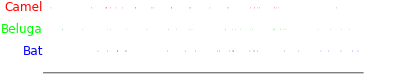

```mathematica
Graphics[{RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Full (Cat) :: Full (corona)

```mathematica
Idt["Cat","F","F"]=Import["/BANK/genome/human_corona/Cat-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["Cat","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["Cat","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["Cat","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["Cat","F","F"]]]];
```

```mathematica
hitLenSource["Cat","F","F"]
```

{27,22,26,24,27,23,23,26,27,22,27,23,22,22,22,22,26,22,26,26,22,26,22}

```mathematica
Max[hitLenSource["Cat","F","F"]]
Min[hitLenSource["Cat","F","F"]]
```

27

22

### Hit sequence

```mathematica
blast["Cat","F","F"]=Import["/BANK/genome/human_corona/Cat-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["Cat","F","F"]=Drop[StringSplit[blast["Cat","F","F"],">"],1];
```

```mathematica
blasteach["Cat","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["Cat","F","F"] ];
```

```mathematica
annotationHit["Cat","F","F"]=Flatten[Map[createAnnotationHit,blasteach["Cat","F","F"]],1];
```

```mathematica
hitCount["Cat","F","F"]=Length[annotationHit["Cat","F","F"]]
```

23

```mathematica
hitFragment["Cat","F","F"]=Table[mergeAnnotationSbjct[annotationHit["Cat","F","F"][[i]]],{i,hitCount["Cat","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["Cat","F","F"]]//Length
```

23

### Hit position

```mathematica
QhitPosition["Cat","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*4},{#[[4]]//ToExpression,200*4}}&,hitFragment["Cat","F","F"]]];
```

```mathematica
Map[Head,QhitPosition["Cat","F","F"],{3}]//Flatten//Tally
```

{{Integer,92}}

```mathematica
QhitLine["Cat","F","F"]={Map[Line,QhitPosition["Cat","F","F"],{1}],Text[Style["Cat",12],{0,200*4},{1,0}]};
```

```mathematica
Graphics[QhitLine["Cat","F","F"]]
```

-Graphics-

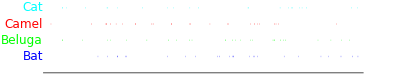

```mathematica
Graphics[{RGBColor[0,1,1],QhitLine["Cat","F","F"],RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Full (C_lupus_familiaris) :: Full (corona)

```mathematica
Idt["C_lupus_familiaris","F","F"]=Import["/BANK/genome/human_corona/C_lupus_familiaris-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["C_lupus_familiaris","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["C_lupus_familiaris","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["C_lupus_familiaris","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["C_lupus_familiaris","F","F"]]]];
```

```mathematica
hitLenSource["C_lupus_familiaris","F","F"]
```

{23,27,23,23,26,22,22,22,22,26,22,22,26,22,22,22,22,22,22,22,34,22,22}

```mathematica
Max[hitLenSource["C_lupus_familiaris","F","F"]]
Min[hitLenSource["C_lupus_familiaris","F","F"]]
```

34

22

### Hit sequence

```mathematica
blast["C_lupus_familiaris","F","F"]=Import["/BANK/genome/human_corona/C_lupus_familiaris-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["C_lupus_familiaris","F","F"]=Drop[StringSplit[blast["C_lupus_familiaris","F","F"],">"],1];
```

```mathematica
blasteach["C_lupus_familiaris","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["C_lupus_familiaris","F","F"] ];
```

```mathematica
annotationHit["C_lupus_familiaris","F","F"]=Flatten[Map[createAnnotationHit,blasteach["C_lupus_familiaris","F","F"]],1];
```

```mathematica
hitCount["C_lupus_familiaris","F","F"]=Length[annotationHit["C_lupus_familiaris","F","F"]]
```

23

```mathematica
hitFragment["C_lupus_familiaris","F","F"]=Table[mergeAnnotationSbjct[annotationHit["C_lupus_familiaris","F","F"][[i]]],{i,hitCount["C_lupus_familiaris","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["C_lupus_familiaris","F","F"]]//Length
```

23

### Hit position

```mathematica
QhitPosition["C_lupus_familiaris","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*5},{#[[4]]//ToExpression,200*5}}&,hitFragment["C_lupus_familiaris","F","F"]]];
```

```mathematica
Map[Head,QhitPosition["C_lupus_familiaris","F","F"],{3}]//Flatten//Tally
```

{{Integer,92}}

```mathematica
QhitLine["C_lupus_familiaris","F","F"]={Map[Line,QhitPosition["C_lupus_familiaris","F","F"],{1}],Text[Style["Dog",12],{0,200*5},{1,0}]};
```

```mathematica
Graphics[QhitLine["C_lupus_familiaris","F","F"]]
```

-Graphics-

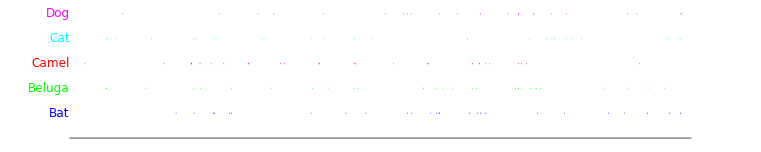

```mathematica
Graphics[{RGBColor[1,0,1],QhitLine["C_lupus_familiaris","F","F"],RGBColor[0,1,1],QhitLine["Cat","F","F"],RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Full (Ferret) :: Full (corona)

```mathematica
Idt["Ferret","F","F"]=Import["/BANK/genome/human_corona/Ferret-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["Ferret","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["Ferret","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["Ferret","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["Ferret","F","F"]]]];
```

```mathematica
hitLenSource["Ferret","F","F"]//Length
```

32

```mathematica
Max[hitLenSource["Ferret","F","F"]]
Min[hitLenSource["Ferret","F","F"]]
```

35

22

### Hit sequence

```mathematica
blast["Ferret","F","F"]=Import["/BANK/genome/human_corona/Ferret-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["Ferret","F","F"]=Drop[StringSplit[blast["Ferret","F","F"],">"],1];
```

```mathematica
blasteach["Ferret","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["Ferret","F","F"] ];
```

```mathematica
annotationHit["Ferret","F","F"]=Flatten[Map[createAnnotationHit,blasteach["Ferret","F","F"]],1];
```

```mathematica
hitCount["Ferret","F","F"]=Length[annotationHit["Ferret","F","F"]]
```

32

```mathematica
hitFragment["Ferret","F","F"]=Table[mergeAnnotationSbjct[annotationHit["Ferret","F","F"][[i]]],{i,hitCount["Ferret","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["Ferret","F","F"]]//Length
```

32

### Hit position

```mathematica
QhitPosition["Ferret","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*6},{#[[4]]//ToExpression,200*6}}&,hitFragment["Ferret","F","F"]]];
```

```mathematica
Map[Head,QhitPosition["Ferret","F","F"],{3}]//Flatten//Tally
```

{{Integer,128}}

```mathematica
QhitLine["Ferret","F","F"]={Map[Line,QhitPosition["Ferret","F","F"],{1}],Text[Style["Ferret",12],{0,200*6},{1,0}]};
```

```mathematica
Graphics[QhitLine["Ferret","F","F"]]
```

-Graphics-

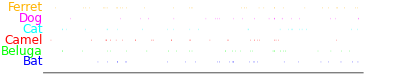

```mathematica
Graphics[{RGBColor[1,0.7,0],QhitLine["Ferret","F","F"],RGBColor[1,0,1],QhitLine["C_lupus_familiaris","F","F"],RGBColor[0,1,1],QhitLine["Cat","F","F"],RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Full (Human) :: Full (corona)

```mathematica
Idt["Human","F","F"]=Import["/BANK/genome/human_corona/Human-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["Human","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["Human","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["Human","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["Human","F","F"]]]];
```

```mathematica
hitLenSource["Human","F","F"]
```

{26,24,26,26,24,24,22,22,28,22,27,22,22,22,23,23,28,26,22,26,27,22,23,22,22,26,22,22,26,22,22,26,26,22,26,22,22,22,22,22,22,22}

```mathematica
Max[hitLenSource["Human","F","F"]]
Min[hitLenSource["Human","F","F"]]
```

28

22

### Hit sequence

```mathematica
blast["Human","F","F"]=Import["/BANK/genome/human_corona/Human-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["Human","F","F"]=Drop[StringSplit[blast["Human","F","F"],">"],1];
```

```mathematica
blasteach["Human","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["Human","F","F"] ];
```

```mathematica
annotationHit["Human","F","F"]=Flatten[Map[createAnnotationHit,blasteach["Human","F","F"]],1];
```

```mathematica
hitCount["Human","F","F"]=Length[annotationHit["Human","F","F"]]
```

42

```mathematica
hitFragment["Human","F","F"]=Table[mergeAnnotationSbjct[annotationHit["Human","F","F"][[i]]],{i,hitCount["Human","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["Human","F","F"]]//Length
```

42

### Hit position

```mathematica
QhitPosition["Human","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*7},{#[[4]]//ToExpression,200*7}}&,hitFragment["Human","F","F"]]];
```

```mathematica
Map[Head,QhitPosition["Human","F","F"],{3}]//Flatten//Tally
```

{{Integer,168}}

```mathematica
QhitLine["Human","F","F"]={Map[Line,QhitPosition["Human","F","F"],{1}],Text[Style["Human",12],{0,200*7},{1,0}]};
```

```mathematica
Graphics[QhitLine["Human","F","F"]]
```

-Graphics-

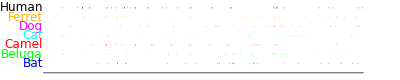

```mathematica
Graphics[{RGBColor[0,0,0],QhitLine["Human","F","F"],RGBColor[1,0.7,0],QhitLine["Ferret","F","F"],RGBColor[1,0,1],QhitLine["C_lupus_familiaris","F","F"],RGBColor[0,1,1],QhitLine["Cat","F","F"],RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Full (Mouse) :: Full (corona)

```mathematica
Idt["Mouse","F","F"]=Import["/BANK/genome/human_corona/Mouse-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["Mouse","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["Mouse","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["Mouse","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["Mouse","F","F"]]]];
```

```mathematica
hitLenSource["Mouse","F","F"]
```

{28,28,24,23,27,23,22,22,23,30,23,22,22,22,22,22,22,22,22,22,22,30,22,22,30,22,22,22,22,26,26,22}

```mathematica
Max[hitLenSource["Mouse","F","F"]]
Min[hitLenSource["Mouse","F","F"]]
```

30

22

### Hit sequence

```mathematica
blast["Mouse","F","F"]=Import["/BANK/genome/human_corona/Mouse-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["Mouse","F","F"]=Drop[StringSplit[blast["Mouse","F","F"],">"],1];
```

```mathematica
blasteach["Mouse","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["Mouse","F","F"] ];
```

```mathematica
annotationHit["Mouse","F","F"]=Flatten[Map[createAnnotationHit,blasteach["Mouse","F","F"]],1];
```

```mathematica
hitCount["Mouse","F","F"]=Length[annotationHit["Mouse","F","F"]]
```

32

```mathematica
hitFragment["Mouse","F","F"]=Table[mergeAnnotationSbjct[annotationHit["Mouse","F","F"][[i]]],{i,hitCount["Mouse","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["Mouse","F","F"]]//Length
```

32

### Hit position

```mathematica
QhitPosition["Mouse","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*8},{#[[4]]//ToExpression,200*8}}&,hitFragment["Mouse","F","F"]]];
```

```mathematica
Map[Head,QhitPosition["Mouse","F","F"],{3}]//Flatten//Tally
```

{{Integer,128}}

```mathematica
QhitLine["Mouse","F","F"]={Map[Line,QhitPosition["Mouse","F","F"],{1}],Text[Style["Mouse",12],{0,200*8},{1,0}]};
```

```mathematica
Graphics[QhitLine["Mouse","F","F"]]
```

-Graphics-

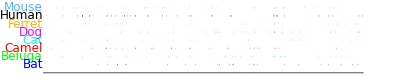

```mathematica
Graphics[{RGBColor[0.3,0.7,1],QhitLine["Mouse","F","F"],RGBColor[0,0,0],QhitLine["Human","F","F"],RGBColor[1,0.7,0],QhitLine["Ferret","F","F"],RGBColor[1,0,1],QhitLine["C_lupus_familiaris","F","F"],RGBColor[0,1,1],QhitLine["Cat","F","F"],RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Full (Rabbit) :: Full (corona)

```mathematica
Idt["Rabbit","F","F"]=Import["/BANK/genome/human_corona/Rabbit-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["Rabbit","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["Rabbit","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["Rabbit","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["Rabbit","F","F"]]]];
```

```mathematica
hitLenSource["Rabbit","F","F"]
```

{24,24,22,22,24,30,22,24,22,23,23,22,23,23,23,31,31,26,30,26,22,22,22,26,22,22}

```mathematica
Max[hitLenSource["Rabbit","F","F"]]
Min[hitLenSource["Rabbit","F","F"]]
```

31

22

### Hit sequence

```mathematica
blast["Rabbit","F","F"]=Import["/BANK/genome/human_corona/Rabbit-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["Rabbit","F","F"]=Drop[StringSplit[blast["Rabbit","F","F"],">"],1];
```

```mathematica
blasteach["Rabbit","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["Rabbit","F","F"] ];
```

```mathematica
annotationHit["Rabbit","F","F"]=Flatten[Map[createAnnotationHit,blasteach["Rabbit","F","F"]],1];
```

```mathematica
hitCount["Rabbit","F","F"]=Length[annotationHit["Rabbit","F","F"]]
```

26

```mathematica
hitFragment["Rabbit","F","F"]=Table[mergeAnnotationSbjct[annotationHit["Rabbit","F","F"][[i]]],{i,hitCount["Rabbit","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["Rabbit","F","F"]]//Length
```

26

### Hit position

```mathematica
QhitPosition["Rabbit","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*9},{#[[4]]//ToExpression,200*9}}&,hitFragment["Rabbit","F","F"]]];
```

```mathematica
Map[Head,QhitPosition["Rabbit","F","F"],{3}]//Flatten//Tally
```

{{Integer,104}}

```mathematica
QhitLine["Rabbit","F","F"]={Map[Line,QhitPosition["Rabbit","F","F"],{1}],Text[Style["Rabbit",12],{0,200*9},{1,0}]};
```

```mathematica
Graphics[QhitLine["Rabbit","F","F"]]
```

-Graphics-

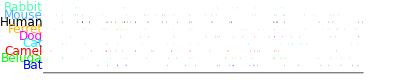

```mathematica
Graphics[{RGBColor[0.3,1,0.7],QhitLine["Rabbit","F","F"],RGBColor[0.3,0.7,1],QhitLine["Mouse","F","F"],RGBColor[0,0,0],QhitLine["Human","F","F"],RGBColor[1,0.7,0],QhitLine["Ferret","F","F"],RGBColor[1,0,1],QhitLine["C_lupus_familiaris","F","F"],RGBColor[0,1,1],QhitLine["Cat","F","F"],RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Full (S_scrofa) :: Full (corona)

```mathematica
Idt["S_scrofa","F","F"]=Import["/BANK/genome/human_corona/S_scrofa-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["S_scrofa","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["S_scrofa","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["S_scrofa","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["S_scrofa","F","F"]]]];
```

```mathematica
hitLenSource["S_scrofa","F","F"]
```

{25,24,22,28,24,22,22,35,23,23,26,23,26,23,23,23,22,22,22,22,23,27,22,26,26,26,22,22,22,22}

```mathematica
Max[hitLenSource["S_scrofa","F","F"]]
Min[hitLenSource["S_scrofa","F","F"]]
```

35

22

### Hit sequence

```mathematica
blast["S_scrofa","F","F"]=Import["/BANK/genome/human_corona/S_scrofa-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["S_scrofa","F","F"]=Drop[StringSplit[blast["S_scrofa","F","F"],">"],1];
```

```mathematica
blasteach["S_scrofa","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["S_scrofa","F","F"] ];
```

```mathematica
annotationHit["S_scrofa","F","F"]=Flatten[Map[createAnnotationHit,blasteach["S_scrofa","F","F"]],1];
```

```mathematica
hitCount["S_scrofa","F","F"]=Length[annotationHit["S_scrofa","F","F"]]
```

30

```mathematica
hitFragment["S_scrofa","F","F"]=Table[mergeAnnotationSbjct[annotationHit["S_scrofa","F","F"][[i]]],{i,hitCount["S_scrofa","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["S_scrofa","F","F"]]//Length
```

30

### Hit position

```mathematica
QhitPosition["S_scrofa","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*10},{#[[4]]//ToExpression,200*10}}&,hitFragment["S_scrofa","F","F"]]];
```

```mathematica
Map[Head,QhitPosition["S_scrofa","F","F"],{3}]//Flatten//Tally
```

{{Integer,120}}

```mathematica
QhitLine["S_scrofa","F","F"]={Map[Line,QhitPosition["S_scrofa","F","F"],{1}],Text[Style["Pig",12],{0,200*10},{1,0}]};
```

```mathematica
Graphics[QhitLine["S_scrofa","F","F"]]
```

-Graphics-

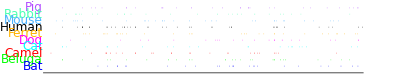

```mathematica
Graphics[{RGBColor[0.7,0.3,1],QhitLine["S_scrofa","F","F"],RGBColor[1,0.3,0.7],RGBColor[0.3,1,0.7],QhitLine["Rabbit","F","F"],RGBColor[0.3,0.7,1],QhitLine["Mouse","F","F"],RGBColor[0,0,0],QhitLine["Human","F","F"],RGBColor[1,0.7,0],QhitLine["Ferret","F","F"],RGBColor[1,0,1],QhitLine["C_lupus_familiaris","F","F"],RGBColor[0,1,1],QhitLine["Cat","F","F"],RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Full (RockPigeon) :: Full (corona)

```mathematica
Idt["RockPigeon","F","F"]=Import["/BANK/genome/human_corona/RockPigeon-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["RockPigeon","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["RockPigeon","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["RockPigeon","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["RockPigeon","F","F"]]]];
```

```mathematica
hitLenSource["RockPigeon","F","F"]
```

{25,25,34,23,23,23,23,22,23,22,22,22,26,26,22,21,22,26,22,22,30,21,21,22,26,21,26,26,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,25,21,21,25,21,25,21,25,21,25,21,21,21,25,25,25,21,25,21,21,25,21,21,21,26,21,29,21,21,21,21,21}

```mathematica
Max[hitLenSource["RockPigeon","F","F"]]
Min[hitLenSource["RockPigeon","F","F"]]
```

34

21

### Hit sequence

```mathematica
blast["RockPigeon","F","F"]=Import["/BANK/genome/human_corona/RockPigeon-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["RockPigeon","F","F"]=Drop[StringSplit[blast["RockPigeon","F","F"],">"],1];
```

```mathematica
blasteach["RockPigeon","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["RockPigeon","F","F"] ];
```

```mathematica
annotationHit["RockPigeon","F","F"]=Flatten[Map[createAnnotationHit,blasteach["RockPigeon","F","F"]],1];
```

```mathematica
hitCount["RockPigeon","F","F"]=Length[annotationHit["RockPigeon","F","F"]]
```

75

```mathematica
hitFragment["RockPigeon","F","F"]=Table[mergeAnnotationSbjct[annotationHit["RockPigeon","F","F"][[i]]],{i,hitCount["RockPigeon","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["RockPigeon","F","F"]]//Length
```

75

### Hit position

```mathematica
QhitPosition["RockPigeon","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*11},{#[[4]]//ToExpression,200*11}}&,hitFragment["RockPigeon","F","F"]]];
```

```mathematica
Map[Head,QhitPosition["RockPigeon","F","F"],{3}]//Flatten//Tally
```

{{Integer,300}}

```mathematica
QhitLine["RockPigeon","F","F"]={Map[Line,QhitPosition["RockPigeon","F","F"],{1}],Text[Style["Rock Pigeon",12],{0,200*11},{1,0}]};
```

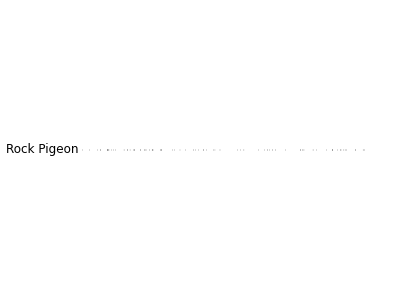

```mathematica
Graphics[QhitLine["RockPigeon","F","F"]]
```

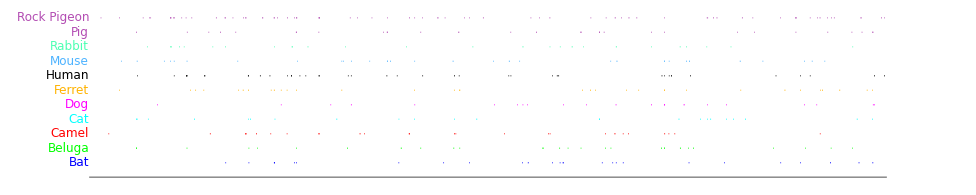

```mathematica
Graphics[{RGBColor[0.7,0.3,0.7],QhitLine["RockPigeon","F","F"],QhitLine["S_scrofa","F","F"],RGBColor[0.3,1,0.7],QhitLine["Rabbit","F","F"],RGBColor[0.3,0.7,1],QhitLine["Mouse","F","F"],RGBColor[0,0,0],QhitLine["Human","F","F"],RGBColor[1,0.7,0],QhitLine["Ferret","F","F"],RGBColor[1,0,1],QhitLine["C_lupus_familiaris","F","F"],RGBColor[0,1,1],QhitLine["Cat","F","F"],RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Full (Turkey) :: Full (corona)

```mathematica
Idt["Turkey","F","F"]=Import["/BANK/genome/human_corona/Turkey-FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["Turkey","F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["Turkey","F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["Turkey","F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["Turkey","F","F"]]]];
```

```mathematica
hitLenSource["Turkey","F","F"]
```

{34,21,21,25,27,22,21,21,21,21,25,21,21,21,21,24,21,24,29,26,27,26,22,21,21,21,21,21,21,23,21,28,26,22,21,25,31,21,26,21,21,26,21,25,21,21,22,21,21,25,21,21,25,21,21,25,21,21,21,21}

```mathematica
Max[hitLenSource["Turkey","F","F"]]
Min[hitLenSource["Turkey","F","F"]]
```

34

21

### Hit sequence

```mathematica
blast["Turkey","F","F"]=Import["/BANK/genome/human_corona/Turkey-FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["Turkey","F","F"]=Drop[StringSplit[blast["Turkey","F","F"],">"],1];
```

```mathematica
blasteach["Turkey","F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["Turkey","F","F"] ];
```

```mathematica
annotationHit["Turkey","F","F"]=Flatten[Map[createAnnotationHit,blasteach["Turkey","F","F"]],1];
```

```mathematica
hitCount["Turkey","F","F"]=Length[annotationHit["Turkey","F","F"]]
```

60

```mathematica
hitFragment["Turkey","F","F"]=Table[mergeAnnotationSbjct[annotationHit["Turkey","F","F"][[i]]],{i,hitCount["Turkey","F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["Turkey","F","F"]]//Length
```

60

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["Turkey","F","F"]];
```

```mathematica
hitFragment["Turkey","F","F"];
```

### Hit position

```mathematica
QhitPosition["Turkey","F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*12},{#[[4]]//ToExpression,200*12}}&,hitFragment["Turkey","F","F"]]];
```

```mathematica
Flatten[Map[Head,QhitPosition["Turkey","F","F"],{3}]]//Tally
```

{{Integer,240}}

```mathematica
QhitLine["Turkey","F","F"]={Map[Line,QhitPosition["Turkey","F","F"],{1}],Text[Style["Turkey",12],{0,200*12},{1,0}]};
```

```mathematica
Graphics[QhitLine["Turkey","F","F"]]
```

-Graphics-

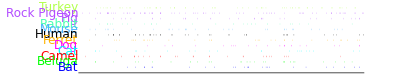

```mathematica
Graphics[{Thick,RGBColor[0.7,1,0.3],QhitLine["Turkey","F","F"],RGBColor[0.7,0.3,1],QhitLine["RockPigeon","F","F"],QhitLine["S_scrofa","F","F"],RGBColor[1,0.3,0.7],RGBColor[0.3,1,0.7],QhitLine["Rabbit","F","F"],RGBColor[0.3,0.7,1],QhitLine["Mouse","F","F"],RGBColor[0,0,0],QhitLine["Human","F","F"],RGBColor[1,0.7,0],QhitLine["Ferret","F","F"],RGBColor[1,0,1],QhitLine["C_lupus_familiaris","F","F"],RGBColor[0,1,1],QhitLine["Cat","F","F"],RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}]}]
```

## Summary

```mathematica
Table[Max[hitLenSource[vertebra[[i]],"F","F"]],{i,Length[vertebra]}]
```

{29,31,32,27,34,35,28,30,31,35,34,34}

```mathematica
QhitRegion["Bat","F","F"]=ToExpression[Map[{#[[3]]//ToExpression,#[[4]]//ToExpression}&,hitFragment["Bat","F","F"]]]
```

{{6932,6960},{7692,7714},{17756,17778},{7764,7786},{22476,22498},{27782,27808},{20008,20030},{16446,16472},{11600,11621},{17759,17780},{16241,16262},{28847,28872},{5979,6000},{25917,25938},{14241,14262},{13282,13303},{17643,17664},{6927,6952},{29366,29391},{17362,17383},{19222,19243},{26655,26676},{19747,19768},{23799,23820},{5112,5133},{19619,19640}}

```mathematica
QhitRegionVt=Table[QhitRegion[vertebra[[i]],"F","F"]=ToExpression[Map[{#[[3]]//ToExpression,#[[4]]//ToExpression}&,hitFragment[vertebra[[i]],"F","F"]]],{i,Length[vertebra]}];
```

```mathematica
QhitCount=(QhitRegionVtFl=Flatten[QhitRegionVt,1])//Length
```

424

```mathematica
AbsoluteTiming[QhitTable=ParallelTable[inRegion[QhitRegionVtFl[[i]],j],{j,len["corona"]},{i,QhitCount}];]
```

{6.97103,Null}

```mathematica
(*AbsoluteTiming[QhitTable=Table[inRegion[QhitRegionVtFl[[i]],j],{j,len["corona"]},{i,QhitCount}];]*)
```

```mathematica
homologCount=Map[Total,QhitTable];
```

```mathematica
homologCount//Max
```

14

```mathematica
Position[homologCount,homologCount//Max]
```

{{21573},{21574},{21575},{21576},{21577},{21578},{21579},{21580},{21581},{21582},{21583},{21584}}

```mathematica
homologuePositionS=Position[homologCount,x_/;x≥5];
```

```mathematica
homologueNucNo=Split[homologuePositionS//Flatten,(#2-#1)<5&]
```

{{1787,1788,1789,1790,1791,1792,1793},{3047,3048,3049,3050,3051,3052,3053,3054,3055,3056,3057,3058,3059,3060,3061,3062,3063,3064,3065,3066,3067},{5866,5867,5868,5869,5870,5871,5872,5873,5874,5875,5876,5877,5878,5879,5880,5881,5882,5883,5884},{6944,6945,6946,6947,6948,6949,6950,6951,6952,6956,6957,6958,6959,6960},{7425,7426,7427,7428,7429,7430},{7764,7765,7766,7767,7768,7769,7770,7771,7772,7773,7774,7775,7776,7777,7778,7779,7780,7781,7782,7783,7784,7785,7786},{8607,8608,8609,8610,8611,8612,8613,8614,8615,8616,8617,8618,8619,8620,8621,8622,8623,8624,8625,8626,8627,8628,8629,8630,8631,8632},{11167,11168,11169,11170,11171,11172,11173,11174,11175,11176,11177,11178,11179,11180,11181,11182,11183,11184,11185,11186},{12198,12199,12200,12201,12202,12203},{19121,19122,19123,19124,19125,19126,19127,19128,19129,19130,19131,19132,19133,19134},{21564,21565,21566,21567,21568,21569,21570,21571,21572,21573,21574,21575,21576,21577,21578,21579,21580,21581,21582,21583,21584,21585,21586,21587},{22389,22390,22391,22392,22393,22394,22395,22396,22397,22398,22399,22400,22401,22402,22403,22404,22405},{26495,26496,26497,26498,26499,26500},{29375,29376,29377,29378,29379}}

```mathematica
homologueSeq=Map[{homologCount[[#[[1]];;#[[-1]]]],#[[1]],StringJoin[StringPart[fasta["corona"][[1]],#[[1]];;#[[-1]]]],#[[-1]]}&,homologueNucNo]
```

{{{5,5,6,6,6,5,5},1787,AATTTTA,1793},{{5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,5,5},3047,GATGAGGATGAAGAAGAAGGT,3067},{{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},5866,CTACAAAGAAAACAGTTAC,5884},{{7,6,6,6,6,6,6,6,6,4,4,4,5,5,5,5,5},6944,ATAAATATTATAATTTG,6960},{{5,5,5,5,5,5},7425,TTGCAT,7430},{{5,5,5,6,6,6,6,6,6,7,7,7,6,6,6,6,6,6,6,6,6,6,5},7764,CCATCCATCTTTACTTTGATAAA,7786},{{5,6,6,7,7,8,8,8,8,9,9,9,9,9,9,9,9,7,7,6,6,6,6,6,5,5},8607,TTTTTGTTGCTGCTATTTTCTATTTA,8632},{{6,7,7,7,7,7,7,7,6,7,7,6,6,6,6,6,6,6,5,5},11167,ATTTCTCTGTTTGTTTTTGT,11186},{{5,5,5,5,5,5},12198,AAAAGT,12203},{{6,6,6,6,6,6,6,6,6,6,6,6,6,6},19121,ATAAAATAGAAGAA,19134},{{8,9,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,13,7,6},21564,TGTTTGTTTTTCTTGTTTTATTGC,21587},{{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},22389,TATTAAAATATAATGAA,22405},{{5,5,5,5,5,5},26495,TTTTCT,26500},{{5,5,5,5,5},29375,CCTAA,29379}}

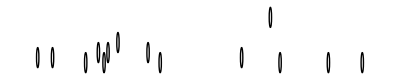

```mathematica
Graphics[freqHC=Map[Circle[{#[[2]],Max[#[[1]]]*50+2700},100]&,homologueSeq]]
```

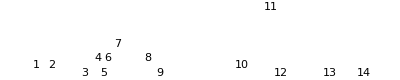

```mathematica
Graphics[freqHT=MapIndexed[Text[#2[[1]],{#[[2]],Max[#[[1]]]*50+2700}]&,homologueSeq]]
```

```mathematica
Nearest[Map[#[[1]]&,slefCorrCount]->slefCorrCount,homologueSeq[[1]][[2]]]
```

{{1785,26}}

```mathematica
Table[Nearest[Map[#[[1]]&,slefCorrCount]->slefCorrCount,homologueSeq[[i]][[2]]],{i,Length[homologueSeq]}]
```

{{{1785,26}},{{3045,20}},{{5865,16}},{{6945,16}},{{7425,20}},{{7765,17}},{{8605,10}},{{11165,13}},{{12200,17}},{{19120,13}},{{21565,21}},{{22390,25}},{{26495,7}},{{29375,10}}}

### Plot

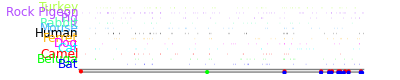

```mathematica
Graphics[{Thick,RGBColor[0.7,1,0.3],QhitLine["Turkey","F","F"],RGBColor[0.7,0.3,1],QhitLine["RockPigeon","F","F"],QhitLine["S_scrofa","F","F"],RGBColor[1,0.3,0.7],RGBColor[0.3,1,0.7],QhitLine["Rabbit","F","F"],RGBColor[0.3,0.7,1],QhitLine["Mouse","F","F"],RGBColor[0,0,0],QhitLine["Human","F","F"],RGBColor[1,0.7,0],QhitLine["Ferret","F","F"],RGBColor[1,0,1],QhitLine["C_lupus_familiaris","F","F"],RGBColor[0,1,1],QhitLine["Cat","F","F"],RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],Gray,Line[{{1,0},{len["corona"],0}}],cdsLine,cdsSG,cdsEG,cdsMG}]
```

## Virus :: corona

## Full (Virus) :: Full (corona)

```mathematica
Idt["F","F"]=Import["/BANK/genome/human_corona/FULL_FULL_W10.mega.Idt","Text"];
```

```mathematica
len["F","F"]=StringCases[Map[StringSplit[#,","][[1]]&,StringSplit[Idt["F","F"],"\n"]],RegularExpression["[0-9]+/[0-9]+"]];
```

```mathematica
hitLenSource["F","F"]=ToExpression[Map[StringSplit[#,"/"][[2]]&,Flatten[len["F","F"]]]];
```

```mathematica
hitLenSource["F","F"]//Length
```

542

```mathematica
hitLenSourceMax["F","F"]=(hitLenSource["F","F"]//Max)
```

10440

```mathematica
hitLenSourceMin["F","F"]=(hitLenSource["F","F"]//Min)
```

20

```mathematica
BinCounts[hitLenSource["F","F"],{0,500,10}]//Normal
```

{0,0,127,108,95,62,30,14,17,9,8,9,7,6,5,5,2,2,5,0,2,1,1,0,0,1,0,2,0,0,1,1,0,0,2,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0}

```mathematica
Sort[Tally[hitLenSource["F","F"]//ToExpression]];
```

### Hit sequence

```mathematica
blast["F","F"]=Import["/BANK/genome/human_corona/FULL_FULL_W10.mega","Text"];
```

```mathematica
blastsplit["F","F"]=Drop[StringSplit[blast["F","F"],">"],1];
```

```mathematica
blasteach["F","F"]=Map[StringSplit[#,"Score "]&,blastsplit["F","F"] ];
```

```mathematica
(Map[Length[#]&,blasteach["F","F"]]-1)//Total
```

542

```mathematica
annotationHit["F","F"]=Flatten[Map[createAnnotationHit,blasteach["F","F"]],1];
```

```mathematica
hitCount["F","F"]=Length[annotationHit["F","F"]]
```

542

```mathematica
hitFragment["F","F"]=Table[mergeAnnotationSbjct[annotationHit["F","F"][[i]]],{i,hitCount["F","F"]}];
```

```mathematica
Map[createFastaFromAnnotationSbjct,hitFragment["F","F"]]//Length
```

542

```mathematica
(selectedFragment["F","F"]=Cases[hitFragment["F","F"],x_List/;StringLength[x[[9]]]≤35])//Length
```

197

### Hit position

#### Total

```mathematica
QhitPosition["F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*-3},{#[[4]]//ToExpression,200*-3}}&,hitFragment["F","F"]]];
```

```mathematica
QhitRegion["F","F"]=ToExpression[Map[{#[[3]]//ToExpression,#[[4]]//ToExpression}&,hitFragment["F","F"]]];
```

```mathematica
QhitCountVr=Length[QhitRegion["F","F"]]
```

542

```mathematica
AbsoluteTiming[QhitTableVr=ParallelTable[inRegion[QhitRegion["F","F"][[i]],j],{j,len["corona"]},{i,QhitCountVr}];]
```

{4.80831,Null}

```mathematica
(*AbsoluteTiming[QhitTableVr=Table[inRegion[QhitRegion["F","F"][[i]],j],{j,len["corona"]},{i,QhitCountVr}];]*)
```

```mathematica
homologCountVr=Map[Total,QhitTableVr];
```

```mathematica
Max[homologCountVr]
```

37

```mathematica
Position[homologCountVr,Max[homologCountVr]]
```

{{15286},{15287},{15288},{15289},{15290},{15291},{15292},{15293},{15294},{15295},{15296},{15297},{15298},{15299},{15300},{15301},{15302},{15303},{15304},{15305},{15306},{15307},{15308}}

```mathematica
homologueVrPositionS=Position[homologCountVr,x_/;x≥17];
```

```mathematica
homologueVrNucNo=Split[homologueVrPositionS//Flatten,(#2-#1)<5&];
```

```mathematica
homologueVrSeq=Map[{homologCountVr[[#[[1]];;#[[-1]]]],#[[1]],StringJoin[StringPart[fasta["corona"][[1]],#[[1]];;#[[-1]]]],#[[-1]]}&,homologueVrNucNo]
```

{{{17,17,17,17,17,17,18,18,18,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,17,17},14068,CAAGATCTCAATGGTAACTGGTATGATTTCGGTGATT,14104},{{18,18,18,18,18,18,18,18,18,18,18,18},14775,TGGTAATGCTGC,14786},{{19,19,19,19,19,19,20,20,20,20,20,20,19,19,19,19,19,19,21,21,21,23,23,23,23,26,26,27,27,27,29,29,29,29,29,29,32,32,32,32,32,32,32,32,32,32,32,32,32,32,28,28,28,27,27,27,25,25,20,20,20,20,20,19,19,19,19,19,19,19,19,18,18,18,18,18,18,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,17,17,17},15031,ACAAAACGTAATGTCATCCCTACTATAACTCAAATGAATCTTAAGTATGCCATTAGTGCAAAGAATAGAGCTCGCACCGTAGCTGGTGTCTCTAT,15125},{{23,23,23,33,35,35,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,35,33,33,32,32,32,31,30,30,30,30,30,25,24,22},15280,CTTATGGGTTGGGATTATCCTAAATGTGATAGAGCCATGCCTAA,15323},{{17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18},15490,GATGCCACAACTGCTTATGCTAATAGTGTTTTTAACAT,15527},{{17,17,17,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,16,18,18,18,19,19,17,17,17,17,17,17,17,17,17,17,17,17,17,19,19,19,18,18,18,19,19,21,23,23,24,24,24,24,24,24,24,26,26,26,26,26,26,26,26,26,26,26,26,26,26,22,22,22,22,22,22,20,20,20,17},15805,CAAAACAATGTTTTTATGTCTGAAGCAAAATGTTGGACTGAGACTGACCTTACTAAAGGACCTCATGAATTTTGCTCTCAACATACA,15891},{{18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,21,24,25,25,27,27,27,27,27,26,26,26,26,26,26,26,27,27,27,27,27,26,26,26,25,25,25,24,24,24,18,18,18},19276,GGTTGTGATGGTGGCAGTTTGTATGTAAATAAACATGCATTCCACACACC,19325},{{17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,19,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,19,19,19,18,18,18,18,18,18,18,18,18,17,17,17},20850,TATGAGAGTTATACATTTTGGTGCTGGTTCTGATAAAGGAGTTGCACCAGGTAC,20903},{{28,29,29,29,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32},29732,CCGAGGCCACGCGGAGTACGATCGAGTGTACAG,29764}}

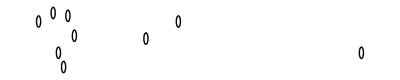

```mathematica
Graphics[freqHVrC=Map[Circle[{#[[2]],(Max[#[[1]]]*-50)-1000},100]&,homologueVrSeq]]
```

```mathematica
freqHVrT=MapIndexed[Text[#2[[1]]+14,{#[[2]],(Max[#[[1]]]*-50)-1000}]&,homologueVrSeq]
```

{Text[15,{14068,-2050}],Text[16,{14775,-1900}],Text[17,{15031,-2600}],Text[18,{15280,-2850}],Text[19,{15490,-1950}],Text[20,{15805,-2300}],Text[21,{19276,-2350}],Text[22,{20850,-2050}],Text[23,{29732,-2600}]}

```mathematica
Table[Nearest[Map[#[[1]]&,slefCorrCount]->slefCorrCount,homologueVrSeq[[i]][[2]]],{i,Length[homologueVrSeq]}]
```

{{{14070,7}},{{14775,13}},{{15030,14}},{{15280,7}},{{15490,10}},{{15805,24}},{{19275,11}},{{20850,10}},{{29730,7}}}

```mathematica
Flatten[Map[Head,QhitPosition["F","F"],{3}]]//Tally
```

{{Integer,2168}}

```mathematica
QhitLine["F","F"]=Map[Line,QhitPosition["F","F"],{1}];
```

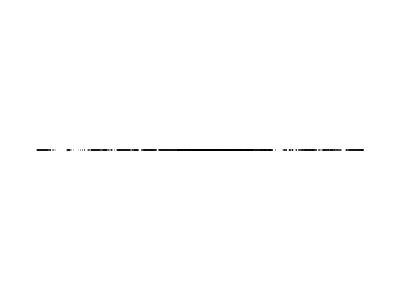

```mathematica
Graphics[QhitLine["F","F"]]
```

#### Selected

```mathematica
SQhitPosition["F","F"]=ToExpression[Map[{{#[[3]]//ToExpression,200*-4},{#[[4]]//ToExpression,200*-4}}&,selectedFragment["F","F"]]];
```

```mathematica
Flatten[Map[Head,SQhitPosition["F","F"],{3}]]//Tally
```

{{Integer,788}}

```mathematica
SQhitLine["F","F"]=Map[Line,SQhitPosition["F","F"],{1}];
```

```mathematica
Graphics[SQhitLine["F","F"]]
```

-Graphics-

## Corona Fourier

Fourier.nb

```mathematica
(*FP["Fourier"]=NotebookOpen[base<>"gitsrc/human_corona/Fourier.nb"]*)
```

```mathematica
(*NotebookImport[FP["Fourier"],"Input"]//ReleaseHold*)
```

Part::partw: {3.7604,1.66811,2.32228,0.997293,0.532181,1.6885,1.20696,1.8966,1.21477,0.892671,2.32523,1.74871,1.42087,«25»,0.853127,1.34297,0.674099,0.451342,0.60511,0.385785,0.803473,0.899549,0.702725,0.895686,1.37705,1.24158,«853»}の部分904は存在しません．

Part::partw: {3.7604,1.66811,2.32228,0.997293,0.532181,1.6885,1.20696,1.8966,1.21477,0.892671,2.32523,1.74871,1.42087,«25»,0.853127,1.34297,0.674099,0.451342,0.60511,0.385785,0.803473,0.899549,0.702725,0.895686,1.37705,1.24158,«853»}の部分905は存在しません．

Part::partw: {3.7604,1.66811,2.32228,0.997293,0.532181,1.6885,1.20696,1.8966,1.21477,0.892671,2.32523,1.74871,1.42087,«25»,0.853127,1.34297,0.674099,0.451342,0.60511,0.385785,0.803473,0.899549,0.702725,0.895686,1.37705,1.24158,«853»}の部分906は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

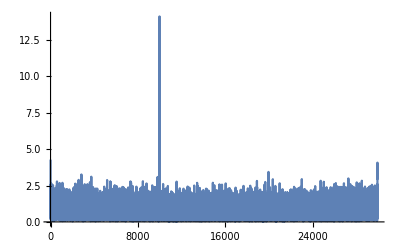
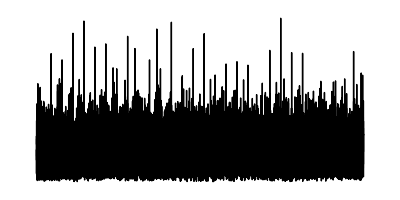
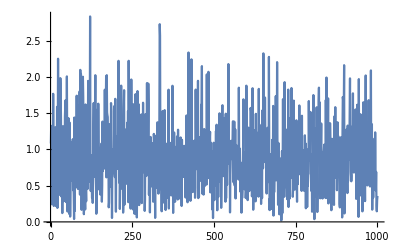
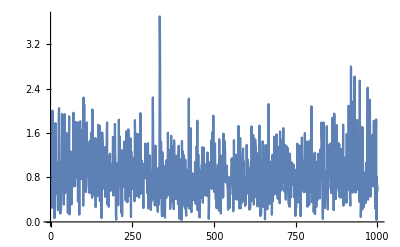
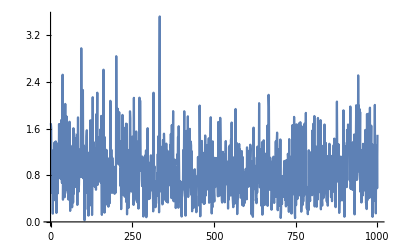
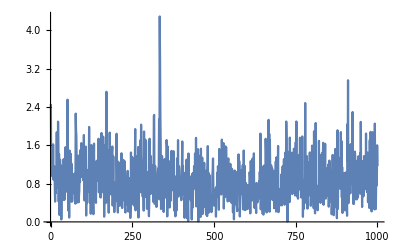
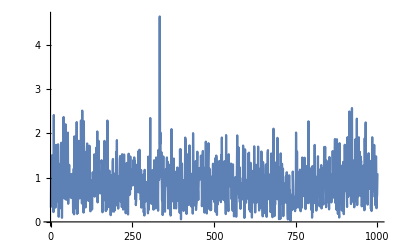
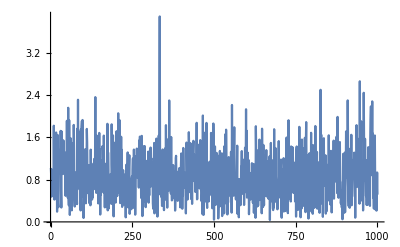
{Null,Null,29903,-Graphics-,10,29903,-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
 |  |  |  |

```mathematica
NotebookImport[base<>"gitsrc/human_corona/Fourier.nb","Input"]//ReleaseHold
```

## Clustering

homological-seg-clustering.nb

## Pattern Analysis

seq-pattern.nb

## Homologue Part

gbk-op.nb

```mathematica
NotebookImport[base<>"gitsrc/human_corona/gbk-op.nb","Input"]//ReleaseHold
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,{{1,AATTTTA,1787,1793,6},{2,GATGAGGATGAAGAAGAAGGT,3047,3067,6},{3,CTACAAAGAAAACAGTTAC,5866,5884,5},{4,ATAAATATTATAATTTG,6944,6960,7},{5,TTGCAT,7425,7430,5},{6,CCATCCATCTTTACTTTGATAAA,7764,7786,7},{7,TTTTTGTTGCTGCTATTTTCTATTTA,8607,8632,9},{8,ATTTCTCTGTTTGTTTTTGT,11167,11186,7},{9,AAAAGT,12198,12203,5},{10,ATAAAATAGAAGAA,19121,19134,6},{11,TGTTTGTTTTTCTTGTTTTATTGC,21564,21587,14},{12,TATTAAAATATAATGAA,22389,22405,5},{13,TTTTCT,26495,26500,5},{14,CCTAA,29375,29379,5}},{{15,CAAGATCTCAATGGTAACTGGTATGATTTCGGTGATT,14068,14104,21},{16,TGGTAATGCTGC,14775,14786,18},{17,ACAAAACGTAATGTCATCCCTACTATAACTCAAATGAATCTTAAGTATGCCATTAGTGCAAAGAATAGAGCTCGCACCGTAGCTGGTGTCTCTAT,15031,15125,32},{18,CTTATGGGTTGGGATTATCCTAAATGTGATAGAGCCATGCCTAA,15280,15323,37},{19,GATGCCACAACTGCTTATGCTAATAGTGTTTTTAACAT,15490,15527,19},{20,CAAAACAATGTTTTTATGTCTGAAGCAAAATGTTGGACTGAGACTGACCTTACTAAAGGACCTCATGAATTTTGCTCTCAACATACA,15805,15891,26},{21,GGTTGTGATGGTGGCAGTTTGTATGTAAATAAACATGCATTCCACACACC,19276,19325,27},{22,TATGAGAGTTATACATTTTGGTGCTGGTTCTGATAAAGGAGTTGCACCAGGTAC,20850,20903,21},{23,CCGAGGCCACGCGGAGTACGATCGAGTGTACAG,29732,29764,32}},{10,14},{10,9},>M,-,{>M,-,-,-,-,-,-,-,-,-},{1787,1788,1789,1790,1791,1792,1793},{>N,N,N<,>F,F,F<,>K},{{>N,N,N<,>F,F,F<,>K},{-,-,-,-,-,-,-},{-,-,-,-,-,-,-},{-,-,-,-,-,-,-},{-,-,-,-,-,-,-},{-,-,-,-,-,-,-},{-,-,-,-,-,-,-},{-,-,-,-,-,-,-},{-,-,-,-,-,-,-},{-,-,-,-,-,-,-}}}

## Final Plot

```mathematica
ticks[1000]=Table[Line[{{i*1000,2800},{i*1000,-3400}}],{i,0,30}];
```

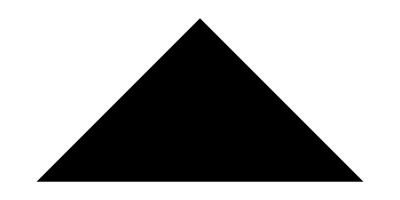

```mathematica
Graphics[mark[1]=Triangle[{{-100,0},{100,0},{0,100}}+Table[{21555,-300},{3}]]]
```

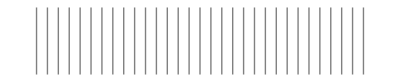

```mathematica
Graphics[{Gray,Thin,ticks[1000]}]
```

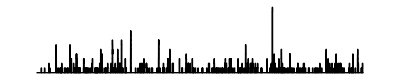

```mathematica
Graphics[homologLineVt=Line[Table[{i,homologCount[[i]]*50+2700},{i,len["corona"]}]]]
```

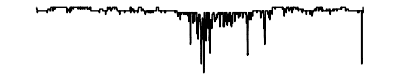

```mathematica
Graphics[homologLineVr=Line[Table[{i,homologCountVr[[i]]*-50-1000},{i,len["corona"]}]]]
```

```mathematica
vstamp={Text["1",{1,-270}],Text["5000",{5000,-270}],Text["10000",{10000,-270}],Text["15000",{15000,-270}],Text["20000",{20000,-270}],Text["25000",{25000,-270}],Text["29903",{29903,-270}]}
```

{Text[1,{1,-270}],Text[5000,{5000,-270}],Text[10000,{10000,-270}],Text[15000,{15000,-270}],Text[20000,{20000,-270}],Text[25000,{25000,-270}],Text[29903,{29903,-270}]}

```mathematica
appendVr={Text[Style["Wuhan-corona genome",12],{-50,10},{1,0}],Text[Style["Coding region (start:    end:    )",12],{-100,-150},{1,0}],Red,Point[{-1500,-150}],Blue,Point[{-500,-150}],Black,Text[Style["Mapped region to 7556 viruses (total)",12],{-50,-600},{1,0}],Text[Style["Mapped region (length <= 35) to viruses",12],{-50,-800},{1,0}],Text[Style["Homologue count in viruses (Max: 37)",12],{-50,-1150},{1,0}]}
```

{Text[Wuhan-corona genome,{-50,10},{1,0}],Text[Coding region (start:    end:    ),{-100,-150},{1,0}],RGBColor[1, 0, 0],Point[{-1500,-150}],RGBColor[0, 0, 1],Point[{-500,-150}],GrayLevel[0],Text[Mapped region to 7556 viruses (total),{-50,-600},{1,0}],Text[Mapped region (length <= 35) to viruses,{-50,-800},{1,0}],Text[Homologue count in viruses (Max: 37),{-50,-1150},{1,0}]}

```mathematica
appendVt={Text[Style["Mapped region to 12 vertebrates",12],{-2200,1400},{1,0}],Text[Style["Homologue count in 12 vertebrates (Max: 14)",12],{-50,2800},{1,0}]}
```

{Text[Mapped region to 12 vertebrates,{-2200,1400},{1,0}],Text[Homologue count in 12 vertebrates (Max: 14),{-50,2800},{1,0}]}

```mathematica
appendFT={Text[Style["Window Fourier (size: 1000 base)",12],{-50,-3700},{1,0}]}
```

{Text[Window Fourier (size: 1000 base),{-50,-3700},{1,0}]}

#### Map only

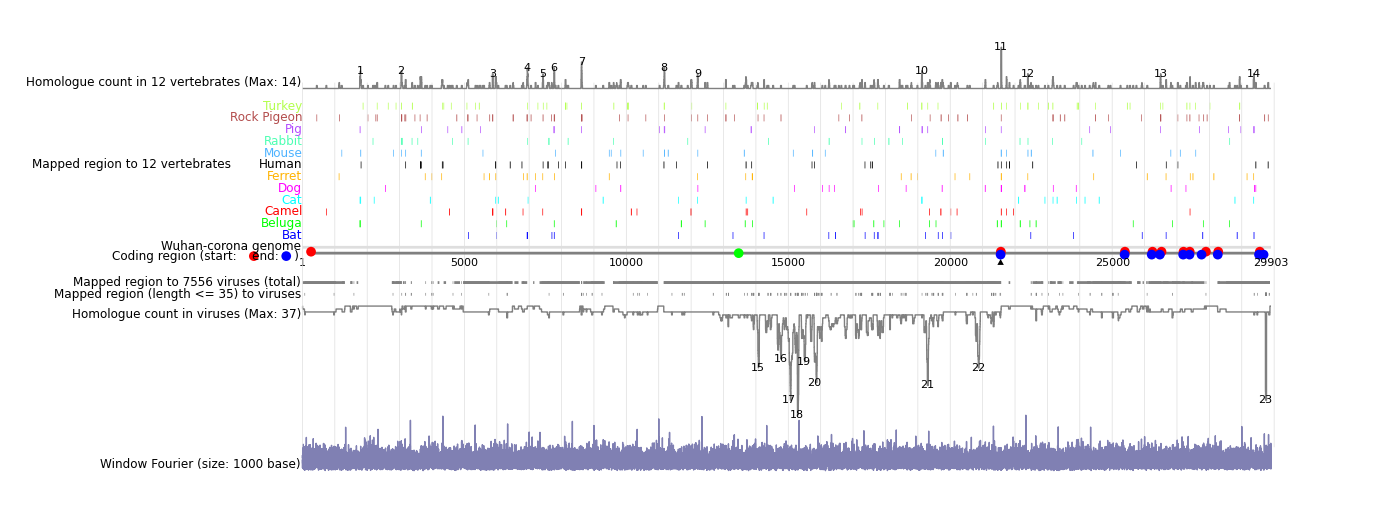

```mathematica
g[1]=Graphics[{AbsoluteThickness[5],RGBColor[0.7,1,0.3],QhitLine["Turkey","F","F"],RGBColor[0.7,0.3,0.3],QhitLine["RockPigeon","F","F"],RGBColor[0.7,0.3,1],QhitLine["S_scrofa","F","F"],RGBColor[0.3,1,0.7],QhitLine["Rabbit","F","F"],RGBColor[0.3,0.7,1],QhitLine["Mouse","F","F"],RGBColor[0,0,0],QhitLine["Human","F","F"],RGBColor[1,0.7,0],QhitLine["Ferret","F","F"],RGBColor[1,0,1],QhitLine["C_lupus_familiaris","F","F"],RGBColor[0,1,1],QhitLine["Cat","F","F"],RGBColor[1,0,0],QhitLine["Camel","F","F"],RGBColor[0,1,0],QhitLine["Beluga","F","F"],RGBColor[{0,0,1}],QhitLine["Bat","F","F"],AbsoluteThickness[2],RGBColor[0.87,0.87,0.87],AbsoluteThickness[0.5],ticks[1000],AbsoluteThickness[2],Line[{{1,0},{len["corona"],0}}],Gray,cdsLine,PointSize->0.005,cdsSG,cdsEG,cdsMG,QhitLine["F","F"],SQhitLine["F","F"],Black,mark[1],AbsoluteThickness[1],Gray,homologLineVt,homologLineVr,Black,vstamp,appendVr,appendVt,appendFT,freqHT,freqHVrT,RGBColor[0.5,0.5,0.7],FourLine},AspectRatio->1/2.7,ImageSize->{1400,450}]
```

#### With homologue table

```mathematica
(*homologVrTbl=MapIndexed[{#2[[1]]+14,#[[3]],#[[2]],#[[4]],Max[#[[1]]]}&,homologueVrSeq]*)
```

```mathematica
(*homologTbl=MapIndexed[{#2[[1]],#[[3]],#[[2]],#[[4]],Max[#[[1]]]}&,homologueSeq]*)
```

```mathematica
(*homologVrTbl=MapIndexed[{#2[[1]]+14,#[[3]],#[[2]],#[[4]],Max[#[[1]]]}&,homologueVrSeq]*)
```

```mathematica
TO[1]=TableForm[homologTbl,TableHeadings->{None, {"No.","homologue","start","end","count"}}]
```

No. | homologue | start | end | count
1 | AATTTTA | 1787 | 1793 | 6
2 | GATGAGGATGAAGAAGAAGGT | 3047 | 3067 | 6
3 | CTACAAAGAAAACAGTTAC | 5866 | 5884 | 5
4 | ATAAATATTATAATTTG | 6944 | 6960 | 7
5 | TTGCAT | 7425 | 7430 | 5
6 | CCATCCATCTTTACTTTGATAAA | 7764 | 7786 | 7
7 | TTTTTGTTGCTGCTATTTTCTATTTA | 8607 | 8632 | 9
8 | ATTTCTCTGTTTGTTTTTGT | 11167 | 11186 | 7
9 | AAAAGT | 12198 | 12203 | 5
10 | ATAAAATAGAAGAA | 19121 | 19134 | 6
11 | TGTTTGTTTTTCTTGTTTTATTGC | 21564 | 21587 | 14
12 | TATTAAAATATAATGAA | 22389 | 22405 | 5
13 | TTTTCT | 26495 | 26500 | 5
14 | CCTAA | 29375 | 29379 | 5

```mathematica
TO[2]=TableForm[homologVrTbl,TableHeadings->{None, {"No.","homologue","start","end","count"}}]
```

No. | homologue | start | end | count
15 | CAAGATCTCAATGGTAACTGGTATGATTTCGGTGATT | 14068 | 14104 | 21
16 | TGGTAATGCTGC | 14775 | 14786 | 18
17 | ACAAAACGTAATGTCATCCCTACTATAACTCAAATGAATCTTAAGTATGCCATTAGTGCAAAGAATAGAGCTCGCACCGTAGCTGGTGTCTCTAT | 15031 | 15125 | 32
18 | CTTATGGGTTGGGATTATCCTAAATGTGATAGAGCCATGCCTAA | 15280 | 15323 | 37
19 | GATGCCACAACTGCTTATGCTAATAGTGTTTTTAACAT | 15490 | 15527 | 19
20 | CAAAACAATGTTTTTATGTCTGAAGCAAAATGTTGGACTGAGACTGACCTTACTAAAGGACCTCATGAATTTTGCTCTCAACATACA | 15805 | 15891 | 26
21 | GGTTGTGATGGTGGCAGTTTGTATGTAAATAAACATGCATTCCACACACC | 19276 | 19325 | 27
22 | TATGAGAGTTATACATTTTGGTGCTGGTTCTGATAAAGGAGTTGCACCAGGTAC | 20850 | 20903 | 21
23 | CCGAGGCCACGCGGAGTACGATCGAGTGTACAG | 29732 | 29764 | 32

```mathematica
gg[1]=Grid[{{"Homologue mapping",""},{g[1],""},{Grid[{{"Frequent homologues (Vertebrates)","Frequent homologues (Viruses)"},{TO[1],TO[2]}},Spacings->{4,1},Alignment->Top]}}]
```

Homologue mapping | 
-Graphics- | 
Frequent homologues (Vertebrates) | Frequent homologues (Viruses)
No. | homologue | start | end | count
1 | AATTTTA | 1787 | 1793 | 6
2 | GATGAGGATGAAGAAGAAGGT | 3047 | 3067 | 6
3 | CTACAAAGAAAACAGTTAC | 5866 | 5884 | 5
4 | ATAAATATTATAATTTG | 6944 | 6960 | 7
5 | TTGCAT | 7425 | 7430 | 5
6 | CCATCCATCTTTACTTTGATAAA | 7764 | 7786 | 7
7 | TTTTTGTTGCTGCTATTTTCTATTTA | 8607 | 8632 | 9
8 | ATTTCTCTGTTTGTTTTTGT | 11167 | 11186 | 7
9 | AAAAGT | 12198 | 12203 | 5
10 | ATAAAATAGAAGAA | 19121 | 19134 | 6
11 | TGTTTGTTTTTCTTGTTTTATTGC | 21564 | 21587 | 14
12 | TATTAAAATATAATGAA | 22389 | 22405 | 5
13 | TTTTCT | 26495 | 26500 | 5
14 | CCTAA | 29375 | 29379 | 5 | No. | homologue | start | end | count
15 | CAAGATCTCAATGGTAACTGGTATGATTTCGGTGATT | 14068 | 14104 | 21
16 | TGGTAATGCTGC | 14775 | 14786 | 18
17 | ACAAAACGTAATGTCATCCCTACTATAACTCAAATGAATCTTAAGTATGCCATTAGTGCAAAGAATAGAGCTCGCACCGTAGCTGGTGTCTCTAT | 15031 | 15125 | 32
18 | CTTATGGGTTGGGATTATCCTAAATGTGATAGAGCCATGCCTAA | 15280 | 15323 | 37
19 | GATGCCACAACTGCTTATGCTAATAGTGTTTTTAACAT | 15490 | 15527 | 19
20 | CAAAACAATGTTTTTATGTCTGAAGCAAAATGTTGGACTGAGACTGACCTTACTAAAGGACCTCATGAATTTTGCTCTCAACATACA | 15805 | 15891 | 26
21 | GGTTGTGATGGTGGCAGTTTGTATGTAAATAAACATGCATTCCACACACC | 19276 | 19325 | 27
22 | TATGAGAGTTATACATTTTGGTGCTGGTTCTGATAAAGGAGTTGCACCAGGTAC | 20850 | 20903 | 21
23 | CCGAGGCCACGCGGAGTACGATCGAGTGTACAG | 29732 | 29764 | 32 |

```mathematica
(*Export[base<>"corona-map.pdf",gg[1]]*)
```

/home/kamano/corona-map.pdf